```mathematica
<<Local`QFTToolKit`
<<PhysicalConstants`
<<Units`
```

```mathematica
DeclareIndexFlavor[{dotted,Orange}]
DeclareIndexFlavor[{undotted,Blue}]
DefineTensorShortcuts[{{η,v,D,F,Λ,H,R,τ,μ,u,Y,Γ,W},1},
{{m,G,h},2},
{{σ,ξ},3}
]
AddBaseIndex[{dotted,{1,2}}]
AddBaseIndex[{undotted,{1,2}}]
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}},{undotted,{1,2}}}

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}},{undotted,{1,2}}}

Lecture 2010.10.11

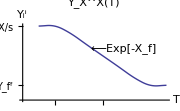
The Dark Matter {X} FreezeOut process.  We assume: 
μ_X->0 (equal number of antiparticles)
For T>m_X the scattering process dominates and {X} is in thermal equilibrium so n_X∼T^3
For T<m_X annihilation processes dominate {XX̄}->{stdModelParticles}
X is cosmologically stable ⟹ ∃ another symmetry
As T falls below m_X we have the picture of Y[T] around FreezeOut temperatures.  We define FreezeOut parameter X_f→m_X^X/T_f
-Graphics-

```mathematica
Get[StringReplace[SaveFile,{"10.11"->"10.08"}]];
Get[StringReplace[SaveFile,{"10.11"->"10.06"}]];

PR1["The Dark Matter {X} FreezeOut process.  We assume: ",
NL,Column[
{"μ_X->0 (equal number of antiparticles)",
"For T>m_X the scattering process dominates and {X} is in thermal equilibrium so n_X∼T^3",
"For T<m_X annihilation processes dominate {XX̄}->{stdModelParticles}",
"X is cosmologically stable ⟹ ∃ another symmetry"},
Frame->All],
NL,"As T falls below m_X we have the picture of Y[T] around FreezeOut temperatures.  We define FreezeOut parameter ",Reverse[subX],
NL,
Show[ListPlot[{{10,10,9,7.5,6,4.5,3,2,2}},Joined->True,InterpolationOrder->2,AxesLabel->{T,Yd[i]},AxesOrigin->{0,0},Ticks->{{{2,md[X],{.6,.0}},
{5,"<slope:-X_f>",{.0,.0}}
},
{{10,Subscript[n, X]/s,{.1,.1}},
{2,Yd[f],{.8,.1}}
}},PlotLabel->Yd[X][T],ImageSize->Small],
Graphics[Text["⟵Exp[-X_f]",{6.3,7}]
]
]
];
```

```mathematica
PR1["Observed amount of Dark Matter.  Assuming a surface of last scatter when {e,p}->{Hydrogen} was at {T_eq} the anisotropy of T_eq/T_0 ⟹ ρ_m[atter]∼5%",imply,
Subscript[Ω, m[atter]]->Subscript[ρ, m[0]]/Subscript[ρ, c[ritical][0]]->Subscript[Ω, Δm] h^2->.110±.006,
NL," where ",Subscript[ρ, c[ritical][0]]," is determined by the Friedman solution now ",{tmp=sFriedmanH[[1]]}," with ",sub=k->0,imply,tmp/.sub/.H->Subscript[H, 0]/.ρ->Subscript[ρ, c][0],
NL,Subscript[H, 0]," is defined ",Subscript[H, 0]->100 [km/(s Mpc)]h,and,h->.72±.03,
NL,"The total fractional energy density must equal ",1==Subscript[Ω, T]->Subscript[Ω, γ[radiation]][.0001]+Subscript[Ω, B[matter]][.044]+Subscript[Ω, DM[DarkMatter]][.22]+Subscript[Ω, DE[DarkEnergy]][.73],
NL,"One can calculate {ρ_B,ρ_DM} from the CMB and nucleogenesis models are sensitive to ρ_B.  These results agree. "
]
```

Observed amount of Dark Matter.  Assuming a surface of last scatter when {e,p}->{Hydrogen} was at {T_eq} the anisotropy of T_eq/T_0 ⟹ ρ_m[atter]∼5% ⇒ Ω_m[atter]→ρ_m[0]/(ρ_(c[ritical][0]))→h^2 Ω_Δm→0.11±0.006
 where ρ_(c[ritical][0]) is determined by the Friedman solution now {H^2→(8 G π ρ)/3-k/a[t]^2} with k→0 ⇒ H_0^2→8/3 G π ρ_c[0]
H_0 is defined H_0→h 100[km/(Mpc s)] and h→0.72±0.03
The total fractional energy density must equal 1==Ω_T→Ω_B[matter][0.044]+Ω_DE[DarkEnergy][0.73]+Ω_DM[DarkMatter][0.22]+Ω_γ[radiation][0.0001]
One can calculate {ρ_B,ρ_DM} from the CMB and nucleogenesis models are sensitive to ρ_B.  These results agree.

```mathematica
PR1[Yd[X][f]," can be computed from ",Subscript[Ω, DM],"?"
]
```

Y_X^X[f] can be computed from Ω_DM?

```mathematica
tmp=dodelson39
tmp=tmp/.{nd[1|2]->nd[X],nd[3|4]->nd[l],0->EQ}
"Assume nd[l][t]==nd[l][EQ] i.e., bath particles "
tmp=tmp/.nd[l][t]->nd[l][EQ]
sub=RuleX[tmpY0,n[t]]/.n->nd[X]/.Y->Yd[X]/.(tmpss/.s->s[t]/.a->a[t])
tmp=MapAt[#/.sub&,tmp,1]//FullSimplify
tmp=tmp//.xPartialDExpand[{S}]/.MapAt[#/.t->t_&,sub,{1,1}]
tmp=tmp//Expand
tmp=Map[a[t]^3#/S&,tmp]//Expand
```

(UnderBar[∂]_t[a[t]^3 n_1^1[t]])/a[t]^3==⟨σ.v⟩ n_1^1[0] n_2^2[0] (-(n_1^1[t] n_2^2[t])/(n_1^1[0] n_2^2[0])+(n_3^3[t] n_4^4[t])/(n_3^3[0] n_4^4[0]))

(UnderBar[∂]_t[a[t]^3 n_X^X[t]])/a[t]^3==⟨σ.v⟩ (n_X^X[EQ])^2 (((n_l^l[t])^2)/((n_l^l[EQ])^2)-((n_X^X[t])^2)/((n_X^X[EQ])^2))

Assume nd[l][t]==nd[l][EQ] i.e., bath particles

(UnderBar[∂]_t[a[t]^3 n_X^X[t]])/a[t]^3==⟨σ.v⟩ (n_X^X[EQ])^2 (1-((n_X^X[t])^2)/((n_X^X[EQ])^2))

{n_X^X[t]→(S Y_X^X[t])/a[t]^3}

(UnderBar[∂]_t[S Y_X^X[t]])/a[t]^3==⟨σ.v⟩ ((n_X^X[EQ])^2-(n_X^X[t])^2)

(S UnderBar[∂]_t[Y_X^X[t]])/a[t]^3==⟨σ.v⟩ ((S^2 (Y_X^X[EQ])^2)/a[EQ]^6-(S^2 (Y_X^X[t])^2)/a[t]^6)

(S UnderBar[∂]_t[Y_X^X[t]])/a[t]^3==(S^2 ⟨σ.v⟩ (Y_X^X[EQ])^2)/a[EQ]^6-(S^2 ⟨σ.v⟩ (Y_X^X[t])^2)/a[t]^6

UnderBar[∂]_t[Y_X^X[t]]==(S a[t]^3 ⟨σ.v⟩ (Y_X^X[EQ])^2)/a[EQ]^6-(S ⟨σ.v⟩ (Y_X^X[t])^2)/a[t]^3

```mathematica
RuleX[tmpY0,n[t]]/.n->nd[X]/.Y->Yd[X]/.(tmpss/.s->s[t]/.a->a[t]);
PR1[
"At the cross-over from radiation dominated to matter dominated {ρ_rad[EQ]==ρ_matter[EQ]} we have ",

tmp={tmpρrad}=={Map[md[X]#&,sub[[1]]]}/.t->EQ,Yield,
tmp=Map[#[[1,2]]&,tmp],Yield,
tmp=tmp/.tmps/.a[EQ]->a,Yield,
tmp1=Solve[tmp,Yd[X][EQ]][[1,1]]/.T->Subscript[T, EQ]/.t->EQ,yield,
tmp1=Map[3/4#&,Reverse[RuleX[tmp1,Subscript[T, EQ]][[1]]]],
NL,"Assuming that ",{tmp1}," is the FreezeOut value where T_EQ->1[eV] and using ",
tmpYf,Yield,
tmp=Map[md[X]#&,tmpYf],
" we can estimate the value of ",BraKet[σ.v],
".  (Note that it is independent of ",Md[X],".)",
NL,
tmp=tmp1[[2]]->tmp[[2]],imply,
Framed[
tmpσv=RuleX[tmp,BraKet[σ.v]][[1]]
]
];
```

At the cross-over from radiation dominated to matter dominated {ρ_rad[EQ]==ρ_matter[EQ]} we have {ρ_rad[T]→1/30 π^2 T^4 g_★}=={m_X^X n_X^X[EQ]→(S m_X^X Y_X^X[EQ])/a[EQ]^3}
→ 1/30 π^2 T^4 g_★==(S m_X^X Y_X^X[EQ])/a[EQ]^3
→ 1/30 π^2 T^4 g_★==2/45 π^2 T^3 g_★ m_X^X Y_X^X[EQ]
→ Y_X^X[EQ]→(3 T_EQ)/(4 m_X^X) ⟶ m_X^X Y_X^X[EQ]→(3 T_EQ)/4
Assuming that {m_X^X Y_X^X[EQ]→(3 T_EQ)/4} is the FreezeOut value where T_EQ->1[eV] and using Y_f^f→(45 X_f)/(2 π^2 ⟨σ.v⟩ g_★ M_p1 m_X^X)
→ m_X^X Y_f^f→(45 X_f)/(2 π^2 ⟨σ.v⟩ g_★ M_p1) we can estimate the value of ⟨σ.v⟩.  (Note that it is independent of Md[X].)
(3 T_EQ)/4→(45 X_f)/(2 π^2 ⟨σ.v⟩ g_★ M_p1) ⇒ ⟨σ.v⟩→(30 X_f)/(π^2 g_★ M_p1 T_EQ)

```mathematica
PR1["Estimate coefficients",
NL,
tmp=tmpσv/.{Subscript[M, p_]->Convert[PlanckMass SpeedOfLight^2,Giga ElectronVolt],Subscript[T, EQ]-> 10^-9 Giga ElectronVolt},
NL,"This estimate does not exclude the WeakScale processes {X,X̄}-{V|ϕ}->{f,f̄} with associated mass 20000 GeV.",
NL,"If m_X>>m_f and if m_Y>m_X (heavy propagator) then the production rate can be estimated: ",
BraKet[σ.v]∼ 1/(8π)g^4/Subscript[m, X]^2(Subscript[m, X]/Subscript[m, Y])^4
];
```

Estimate coefficients
⟨σ.v⟩→(2.48968×10^-10 X_f)/(ElectronVolt^2 Giga^2 g_★)
This estimate does not exclude the WeakScale processes {X,X̄}-{V|ϕ}->{f,f̄} with associated mass 20000 GeV.
If m_X>>m_f and if m_Y>m_X (heavy propagator) then the production rate can be estimated: ⟨σ.v⟩∼(g^4 m_X^2)/(8 π m_Y^4)

```mathematica
PR1["If SUSY particles are the source of DarkMatter, the candidates would be the lightest state due to R-parity stability.  Possible candidates ",
{b̃,OverTilde[Wd[3]],OverTilde[hdu[u,0]],OverTilde[hdu[d,0]],ν̃,g̃,g̃ u u},
NL,"Must consider mass mixing as in hep-ph/9709356:Martin(7.30).  Yukawa gauge interactions {{h_u->(h_u,↑x)->b̃} complicates interpretation.  LightestSuperPartner may be linear combination ",NL, χ̃->c[1] b̃+c[2] w̃+c[3] Subscript[h̃, u]+c[4] Subscript[h̃, d],".","  Other candidates include the gravatino and axion.  Examine ∨bino b̃ as candidate.  
"
]
```

If SUSY particles are the source of DarkMatter, the candidates would be the lightest state due to R-parity stability.  Possible candidates {b̃,OverTilde[W_3^3],OverTilde[h_u0^u0],OverTilde[h_d0^d0],ν̃,g̃,u^2 g̃}
Must consider mass mixing as in hep-ph/9709356:Martin(7.30).  Yukawa gauge interactions {{h_u->(h_u,↑x)->b̃} complicates interpretation.  LightestSuperPartner may be linear combination 
χ̃→c[1] b̃+c[2] w̃+c[4] (h̃)_d+c[3] (h̃)_u.  Other candidates include the gravatino and axion.  Examine bion b̃ as candidate.